The Quantum Stochastic Master Equation (SME) describes the evolution of an open quantum system interacting with its environment in a probabilistic manner. It extends the Lindblad master equation by incorporating stochastic noise, often modeled using quantum Wiener or Poisson processes. QSMEs are crucial for understanding decoherence, quantum measurement dynamics, and feedback control in quantum information processing.

Dynamical equation of the quantum system:

ⅆρ=ⅆt(-i[H,ρ]+∑_i Γ_i(V_i ρ V_i^†-1/2{V_i^†V_i,ρ})+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ}))+∑_i √η_i ⅆ w_i √γ_i(L_i ρ+ρ L_i^†-Tr[L_i ρ+ρ L_i^†]ρ)

There are jump/Lindblad operators due to the environment, denoted by V_i, that contribute  only as decoherence term in the dynamical equation (deterministic) with the decoherence rate Γ_i.
There are jump/Lindblad operators due to the monitoring of the system (with a corresponding readout), denoted by L_i, that contribute as decoherence terms and also stochastic terms in the dynamical equation, with the decoherence rate of γ_i and the measurement channel efficiency of η_i. Their corresponding output signal reads as

ⅆ R_j=√η_i ⅆt Tr(L_i ρ+ρL_i^†)+ⅆ w_i

We have implemented the efficient numerical scheme proposed in this paper:  https://arxiv.org/pdf/1410.5345
The main function for simulation is the following one:

𝒯[ρ_0,H,L,η,V,δt,t_f]
The function for manual evolution, with ρ the initial state, H the Hamiltonian, L the list of jump operators being monitored (and the evolution is conditioned upon their corresponding readout currents), η the readout efficiency, V the list of jump operator not being monitors (e.g. environmental noise; by default it is None), δt the time increment and t_f the final time.

We call it manual evolution because we do not use numerical features of Mathematica such as NDSolve or ItoProcess. The main reason for that is we were not able to using those functionalities while preserving important features of a Bloch sphere dynamics.

The readout currents are sowed in 𝒯.

Below examples are taken from Prof. Gabriel T. Landi’s melt notebook.

### ℒ[ρ]=-i [Ωσ_x,ρ] + γ D[σ_z] and γ >> Ω

Hamiltonian, jump operators and damping rates:

ℒ[ρ]=-i [Ωσ_x,ρ] + γ D[σ_z]

```mathematica
SeedRandom[1];
Ω = 1.0;H = Ω QuantumOperator["X"];
```

Jump operators and damping rates (note they are List):

```mathematica
γs ={2.0};
Ls ={QuantumOperator["Z"]};
```

Time increment and final time:

```mathematica
δt = 0.005;
tf = 20.;
```

Initial state:

```mathematica
ρ0=QuantumState["0"];
```

Solve the Lindblad master equation for the density matrix: ∂_t ρ=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ})

```mathematica
ρt=QuantumEvolve[H,Ls->γs,ρ0,{t,0,tf}]
```

QuantumState[…]

```mathematica
MatchQ[{1},None]
```

False

```mathematica
trajectory=𝒯[ρ0,H,√γs Ls,δt,tf];//AbsoluteTiming
```

{0.151829,Null}

Check if any un-physical state:

```mathematica
PositiveSemidefiniteMatrixQ/@trajectory//Tally
```

{{True,4001}}

```mathematica
bloch=Table[Re@Tr[#.PauliMatrix[i]],{i,3}]&/@trajectory;
```

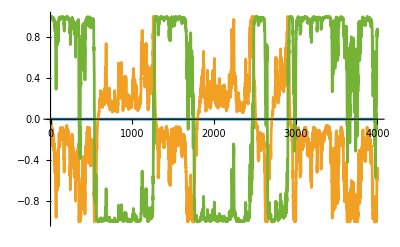

```mathematica
ListLinePlot[Transpose[bloch]]
```

For each trajectory, find Bloch vector:

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ListLinePlot3D[bloch]]
```

-Graphics3D-

### ℒ[ρ]=-i [Ωσ_x,ρ] + γ D[σ_z] and γ << Ω

Hamiltonian, jump operators and damping rates:

ℒ[ρ]=-i [Ωσ_x,ρ] + γ D[σ_z]

```mathematica
SeedRandom[1];
Ω = 1.0;H = Ω QuantumOperator["X"];
```

Jump operators and damping rates (note they are List):

```mathematica
γs ={.1};
Ls ={QuantumOperator["Z"]};
```

Time increment and final time:

```mathematica
δt = 0.005;
tf = 20.;
```

Initial state:

```mathematica
ρ0=QuantumState["0"];
```

Solve the Lindblad master equation for the density matrix: ∂_t ρ=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ})

```mathematica
ρt=QuantumEvolve[H,Ls->γs,ρ0,{t,0,tf}]
```

QuantumState[…]

Plot the evolution:

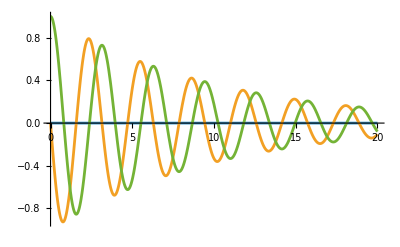

```mathematica
Plot[Evaluate@Re@ρt[t]["BlochVector"],{t,0,tf},PlotRange->All]
```

```mathematica
average=Table[Evaluate@Re[ρt[t]["BlochVector"]],{t,0,tf,δt}]//Transpose;
```

```mathematica
trajectory=𝒯[ρ0,H,√γs Ls,δt,tf];//AbsoluteTiming
```

{0.140214,Null}

Check if any un-physical state:

```mathematica
PositiveSemidefiniteMatrixQ/@trajectory//Tally
```

{{True,4001}}

```mathematica
bloch=Table[Re@Tr[#.PauliMatrix[i]],{i,3}]&/@trajectory;
```

Visualize them:

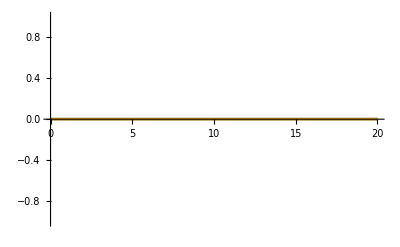
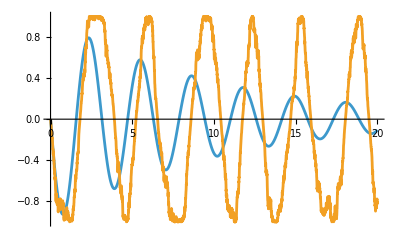
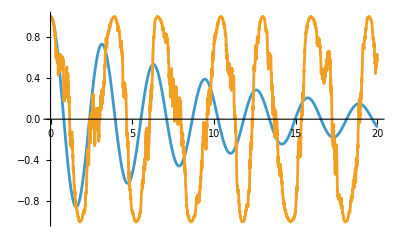

```mathematica
Table[ListLinePlot[Transpose[{Range[0,tf,δt],#}]&/@{average[[i]],Transpose@bloch[[All,i]]}],{i,3}]
```

### Diffusion for spontaneous emission

Hamiltonian, jump operators and damping rates:

```mathematica
SeedRandom[1];
Δ=1.;Ω=2.;
H = 1/2(Ω QuantumOperator["X"]+Δ QuantumOperator["Z"]);
```

Jump operators and damping rates (note they are List):

```mathematica
γs ={.2};
Ls ={QuantumOperator["J-"]};
```

Time increment and final time:

```mathematica
δt = 0.01;
tf = 10.;
```

Initial state:

```mathematica
ρ0=QuantumState["+"];
```

Solve the Lindblad master equation for the density matrix: ∂_t ρ=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ})

```mathematica
ρt=QuantumEvolve[H,Ls->γs,ρ0,{t,0,tf}]
```

QuantumState[…]

Plot the evolution:

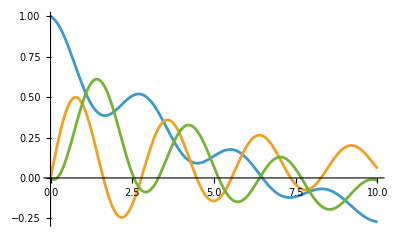

```mathematica
Plot[Evaluate@Re@ρt[t]["BlochVector"],{t,0,tf},PlotRange->All]
```

```mathematica
average=Table[Evaluate@Re[ρt[t]["BlochVector"]],{t,0,tf,δt}]//Transpose;
```

```mathematica
trajectory=Table[𝒯[ρ0,H,√γs Ls,δt,tf],200];//AbsoluteTiming
```

{6.35266,Null}

Check if any un-physical state:

```mathematica
Map[PositiveSemidefiniteMatrixQ]/@trajectory//Flatten//Tally
```

{{True,200200}}

```mathematica
bloch=Map[Table[Re@Tr[#.PauliMatrix[i]],{i,3}]&]/@trajectory;
```

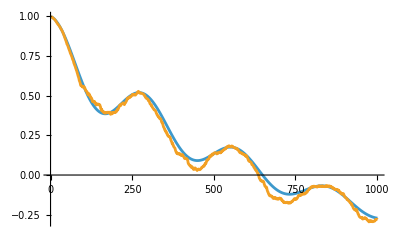
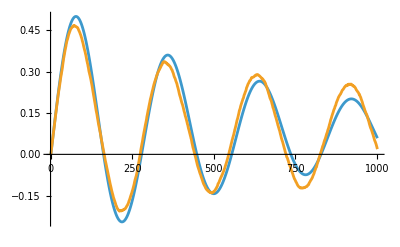
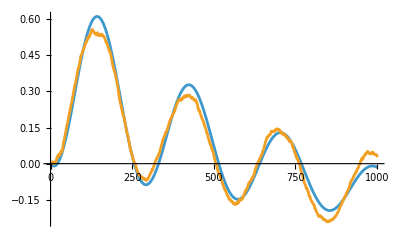

```mathematica
Table[ListLinePlot[{average[[i]],Mean[(Transpose/@bloch)[[All,i,All]]]}],{i,3}]
```

### Reproducing Fig. 4.6 of Wiseman and Milburn

#### Exp #1

Hamiltonian, jump operators and damping rates:

```mathematica
SeedRandom[1];
Δ=0;Ω=3.;
H = 1/2(Ω QuantumOperator["Y"]+Δ QuantumOperator["Z"]);
```

Jump operators and damping rates (note they are List):

```mathematica
γs ={1};
Ls ={QuantumOperator["J-"]};
```

Time increment and final time:

```mathematica
δt = 0.01;
tf = 10.;
```

Initial state:

```mathematica
ρ0=QuantumState["+"];
```

Solve the Lindblad master equation for the density matrix: ∂_t ρ=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ})

```mathematica
ρt=QuantumEvolve[H,Ls->γs,ρ0,{t,0,tf}]
```

QuantumState[…]

Plot the evolution:

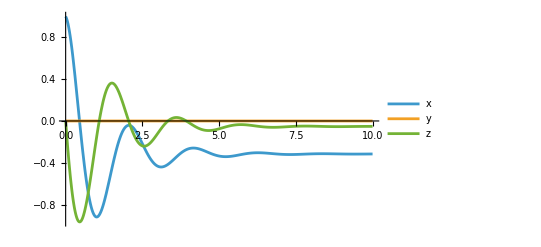

```mathematica
Plot[Evaluate@Re@ρt[t]["BlochVector"],{t,0,tf},PlotRange->All,PlotLegends->{"x","y","z"}]
```

Manual simulation:

```mathematica
trajectory=𝒯[ρ0,H,√γs Ls,δt,tf];
```

Check if any un-physical state:

```mathematica
PositiveSemidefiniteMatrixQ/@trajectory//Tally
```

{{True,1001}}

```mathematica
bloch=Table[Re@Tr[#.PauliMatrix[i]],{i,3}]&/@trajectory;
```

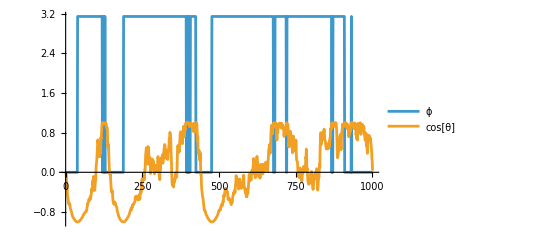

```mathematica
ListLinePlot[Transpose[{ArcTan[#1,#2],#3}&@@@bloch],PlotLegends->{"ϕ","cos[θ]"}]
```

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ListLinePlot3D[bloch]]
```

-Graphics3D-

#### Exp #2

Hamiltonian, jump operators and damping rates:

```mathematica
SeedRandom[1];
Δ=0;Ω=3.;
H = 1/2(Ω QuantumOperator["Y"]+Δ QuantumOperator["Z"]);
```

Jump operators and damping rates (note they are List):

```mathematica
γs ={1};
Ls ={Exp[ⅈ π/2]QuantumOperator["J-"]};
```

Time increment and final time:

```mathematica
δt = 0.01;
tf = 10.;
```

Initial state:

```mathematica
ρ0=QuantumState["+"];
```

Solve the Lindblad master equation for the density matrix: ∂_t ρ=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ})

```mathematica
ρt=QuantumEvolve[H,Ls->γs,ρ0,{t,0,tf}]
```

QuantumState[…]

Plot the evolution:

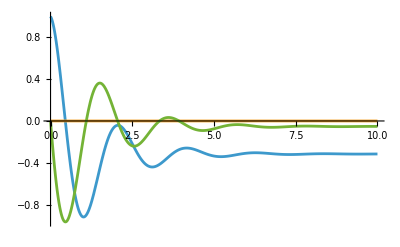

```mathematica
Plot[Evaluate@Re@ρt[t]["BlochVector"],{t,0,tf},PlotRange->All]
```

Manual

```mathematica
trajectory=𝒯[ρ0,H,√γs Ls,δt,tf];
```

Check if any un-physical state:

```mathematica
PositiveSemidefiniteMatrixQ/@trajectory//Tally
```

{{True,1001}}

```mathematica
bloch=Table[Re@Tr[#.PauliMatrix[i]],{i,3}]&/@trajectory;
```

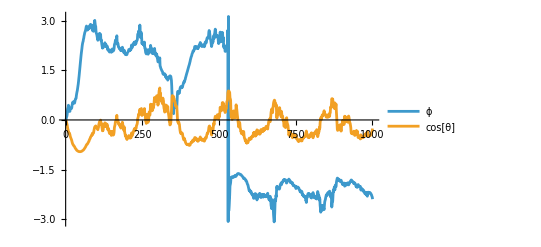

```mathematica
ListLinePlot[Transpose[{ArcTan[#1,#2],#3}&@@@bloch],PlotLegends->{"ϕ","cos[θ]"}]
```

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ListLinePlot3D[bloch]]
```

-Graphics3D-

### Two-point function for the stochastic homodyne current

Hamiltonian, jump operators and damping rates:

```mathematica
SeedRandom[1];
Δ=0;Ω=3.5;
H = 1/2(Ω QuantumOperator["Y"]+Δ QuantumOperator["Z"]);
```

Jump operators and damping rates (note they are List):

```mathematica
γs ={.7};
Ls ={QuantumOperator["J-"]};
```

Time increment and final time:

```mathematica
δt = 0.01;
tf = 4000.;
```

Initial state:

```mathematica
ρ0=QuantumState["0"];
```

Generate trajectory and output currents:

```mathematica
{trajectory,{Is}}=Reap@𝒯[ρ0,H,√γs Ls,δt,tf];
```

Check if any un-physical state:

```mathematica
PositiveSemidefiniteMatrixQ/@trajectory//Tally
```

{{True,400001}}

Since only one jump operator being monitored, only one current:

```mathematica
I1=Re@Transpose[Is][[1]];
```

Two point correlations:

```mathematica
ℱ1=TwoPointCorrelation[Chop@Flatten@Is,Floor[8/δt],δt,4];
ℱ2=TwoPointCorrelation[butterworthFilter[Chop@Flatten@Is,50,δt],Round[8/δt],δt,4];
```

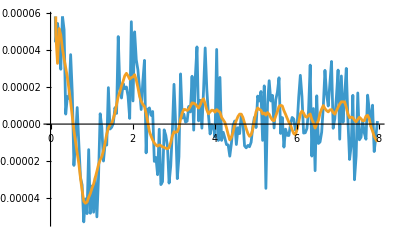

```mathematica
ListLinePlot[{ℱ1,ℱ2}]
```

## Initialization

### Install quantum paclet

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall -> True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

### Manual evolution

```mathematica
ClearAll[𝒯,ℛ]
```

Implementation of https://arxiv.org/pdf/1410.5345
to ensure positivity of ρ

```mathematica
ℛ[ρ_,L_,δt_,δw_,η_]:=MapThread[√#3 Tr[(#1+ConjugateTranspose[#1]).ρ]δt+#2&,{L,δw,η}]
```

```mathematica
𝒯[ρ_,H_,L_,η_:None,V_:None,δt_,tf_]:=
Module[{δw,Lmat,Vmat,Hmat,ρ0,Heff,ηm},
ηm=If[MatchQ[η,None],ConstantArray[1,Length[L]],η];
ρ0=ρ["Computational"]["DensityMatrix"];
Lmat=#["Computational"]["Matrix"]&/@L;
Vmat=#["Computational"]["Matrix"]&/@V;
Hmat=H["Computational"]["Matrix"];
Heff=IdentityMatrix[2]-δt(I Hmat+.5Sum[l.l+ConjugateTranspose[l].l,{l,Lmat}]+If[MatchQ[V,None],0,.5Sum[l.l+ConjugateTranspose[l].l,{l,Vmat}]]);
δw=RandomVariate[NormalDistribution[0,√δt],{Length[L],Floor[tf/δt]}];
FoldList[
Module[{M,st,Υ},
Υ=Total[√ηm Lmat Sow@ℛ[#1,Lmat,δt,#2,ηm]];
M=Heff+.5Υ.Υ+Υ;
st=M.#1.ConjugateTranspose[M]+If[MatchQ[V,None],0,δt Sum[l.#1.ConjugateTranspose[l],{l,Vmat}]]+δt Sum[(1-ηm[[l]])Lmat[[l]].#1.ConjugateTranspose[Lmat[[l]]],{l,Range[Length@Lmat]}];
st/Tr[st]]&,ρ0,Transpose[δw]]]
```

### Two point correlation and Butterworth filter

Gabriel’ s  function :

```mathematica
Clear[TwoPointCorrelation];
TwoPointCorrelation[data_,hmax_,dt_:None,steps_:1]:=Module[{𝒩=Length@data,ave = Mean[data],vec1,M,corr},
vec1 = data⟦1;;𝒩-hmax⟧;
M = Table[data⟦1+i;;𝒩-hmax+i⟧,{i,1,hmax,steps}];
corr=1/𝒩(M.vec1-ave^2);
If[dt===None,corr,{dt Range[1, hmax,steps],corr}ᵀ]
]
```

https://mathematica.stackexchange.com/questions/46500/data-filtering-using-butterworth-filter

```mathematica
Clear[butterworthFilter];
butterworthFilter[data_,ωc_,dt_:1,order_:2]:=Module[{f,b},
f=RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass",order,ωc }],dt],data];
b=RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass",order,ωc }],dt],Reverse[data]];
(f+Reverse[b])/2
]
```